```mathematica
(*R is the radius, interval is [-R,R]*)
startR=0;
endR=5
(*intervals*)
M=1000;
(*sites is intervals + 1*)
sites=M+1;
ϵ=1;
a=1;
(*define m_k (the factor in each element of the matrix*)
mk[j_]=((startR+Δx*j)^3-(startR+Δx*j-Δx)^3)/(3 Δx^2);
(*electron density function*)
ρ[r_]=If[r>=0,1/(π a^3)ⅇ^(-2 r/a),1/(π a^3)ⅇ^(2 r/a)];
(*integrals that come from integrating the electron density and everything*)
int[R_,v_,a1_,a2_]:=NIntegrate[1/ϵ r^2 ρ[r]*v,{r,a1,a2}];
(*interval length*)
Δx=(endR-startR)/M;
(*defines elements*)
linFunc[a_,r_]:=If[r<a,1/Δx(r-a)+1,-1/Δx(r-a)+1];
RealFunction[r_]=If[r>0,1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a)),1/(4π ϵ a^2)(-a^2/r-(-a^2/r-a)ⅇ^(2 r/a))];
boundary[r_]:=If[0≤r<endR/2,Limit[RealFunction[r],r->0],1/(4 π ϵ)1/Abs[r]]
```

5

```mathematica
(*Making a table of elements in the vector on the RHS*)
RHS=Table[int[R,linFunc[i,r],i-Δx,i+Δx],{i,startR+Δx,endR-Δx,Δx}];
```

```mathematica
(*check dimensions*)
b=RHS;
b[[1]]=b[[1]]+mk[1]*boundary[startR]
b[[Length[b]]]=b[[Length[b]]]+mk[sites]*boundary[endR]
Dimensions[b]
(*Remove the first 2 rows and last 2 rows because of boundary conditions?*)
(*check dimen
sions*)
```

39.7092

39.8684

{999}

```mathematica
(*define array of zeroes*)
LHS=ConstantArray[0,{sites,sites}];
(*create a loop to fill in elements*)
For[i=0,i<sites,i++,
If[i+1<=sites&&i>0,LHS[[i+1,i]]=-mk[i]];
If[i+1<=sites&&i>=0,LHS[[i+1,i+1]]=mk[i+1]+mk[i]];
If[i+2<=sites,LHS[[i+1, i+2]]=-mk[i+1]];
]
```

```mathematica
LHS//MatrixForm;
```

```mathematica
(*check dimensions*)
Dimensions[LHS]
```

{1001,1001}

```mathematica
(*check dimensions*)
Dimensions[b]
```

{999}

```mathematica
LHS=Delete[LHS,{{1},{sites}}];
(*delete the first and last columns in the matrix*)
LHS=Drop[LHS,None,{1,1}];
LHS=Drop[LHS,None,{sites-1,sites-1}];
```

```mathematica
Dimensions[LHS]
```

{999,999}

```mathematica
(*solve the system*)
system=LinearSolve[LHS,b];
```

```mathematica
listOfR=Table[startR+Δx*j,{j,1,M-1} ];
```

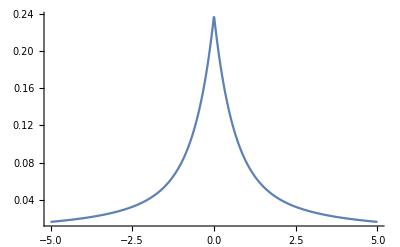

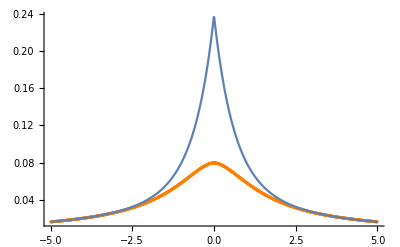

```mathematica
temp1=ListPlot[Transpose[{listOfR,system}],PlotStyle->{Orange}];
temp2=Plot[If[r>0,1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a)),1/(4π ϵ a^2)(-a^2/r-(-a^2/r-a)ⅇ^(2 r/a))],{r,startR,endR},PlotRange->All]
Show[temp1,temp2,PlotRange->All]
```

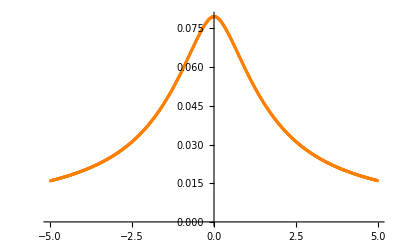

```mathematica
temp1
```

```mathematica
system[[1]]
```

0.0159473

```mathematica
N[boundary[-R]]
```

If[0.≤-1. R<2.5,lim_(-1. R→0.) RealFunction[-1. R],((1. 0.0795775) 1.)/(1. Abs[R])]

```mathematica
system[[Length[system]]]
```

0.0160111

```mathematica
RHS
```

{3.67114×10^-6,3.73031×10^-6,3.7904×10^-6,3.85142×10^-6,3.9134×10^-6,3.97634×10^-6,4.04026×10^-6,4.10517×10^-6,4.1711×10^-6,4.23804×10^-6,4.30603×10^-6,4.37506×10^-6,4.44517×10^-6,4.51637×10^-6,4.58866×10^-6,4.66207×10^-6,4.73662×10^-6,4.81232×10^-6,4.88918×10^-6,4.96723×10^-6,5.04648×10^-6,5.12695×10^-6,5.20866×10^-6,5.29163×10^-6,5.37587×10^-6,5.4614×10^-6,5.54824×10^-6,5.63641×10^-6,5.72594×10^-6,5.81683×10^-6,5.90911×10^-6,6.0028×10^-6,6.09792×10^-6,6.1945×10^-6,6.29254×10^-6,6.39208×10^-6,6.49313×10^-6,6.59571×10^-6,6.69985×10^-6,6.80558×10^-6,6.91291×10^-6,7.02186×10^-6,7.13246×10^-6,7.24474×10^-6,7.35871×10^-6,7.4744×10^-6,7.59184×10^-6,7.71105×10^-6,7.83205×10^-6,7.95487×10^-6,8.07954×10^-6,8.20608×10^-6,8.33453×10^-6,8.46489×10^-6,8.59721×10^-6,8.73151×10^-6,8.86782×10^-6,9.00616×10^-6,9.14657×10^-6,9.28907×10^-6,9.4337×10^-6,9.58047×10^-6,9.72943×10^-6,9.8806×10^-6,0.000010034,0.0000101897,0.0000103477,0.000010508,0.0000106707,0.0000108358,0.0000110034,0.0000111734,0.0000113459,0.000011521,0.0000116986,0.0000118788,0.0000120617,0.0000122472,0.0000124355,0.0000126265,0.0000128203,0.0000130169,0.0000132164,0.0000134188,0.0000136242,0.0000138325,0.0000140438,0.0000142582,0.0000144757,0.0000146964,0.0000149202,0.0000151473,0.0000153776,0.0000156113,0.0000158483,0.0000160887,0.0000163326,0.0000165799,0.0000168308,0.0000170853,0.0000173434,0.0000176052,0.0000178707,0.0000181399,0.000018413,0.00001869,0.0000189709,0.0000192558,0.0000195447,0.0000198376,0.0000201347,0.000020436,0.0000207415,0.0000210513,0.0000213654,0.0000216839,0.0000220069,0.0000223344,0.0000226664,0.0000230031,0.0000233445,0.0000236905,0.0000240414,0.0000243971,0.0000247578,0.0000251234,0.000025494,0.0000258698,0.0000262507,0.0000266368,0.0000270282,0.0000274249,0.0000278271,0.0000282347,0.0000286479,0.0000290667,0.0000294912,0.0000299214,0.0000303575,0.0000307994,0.0000312472,0.0000317011,0.0000321611,0.0000326272,0.0000330996,0.0000335783,0.0000340633,0.0000345549,0.0000350529,0.0000355575,0.0000360688,0.0000365869,0.0000371118,0.0000376436,0.0000381824,0.0000387282,0.0000392812,0.0000398414,0.0000404089,0.0000409838,0.0000415661,0.000042156,0.0000427535,0.0000433587,0.0000439717,0.0000445926,0.0000452214,0.0000458582,0.0000465032,0.0000471564,0.0000478179,0.0000484878,0.0000491661,0.000049853,0.0000505486,0.0000512529,0.000051966,0.000052688,0.000053419,0.0000541591,0.0000549084,0.000055667,0.0000564349,0.0000572123,0.0000579992,0.0000587958,0.0000596021,0.0000604182,0.0000612442,0.0000620803,0.0000629264,0.0000637828,0.0000646494,0.0000655264,0.0000664139,0.000067312,0.0000682208,0.0000691403,0.0000700706,0.0000710119,0.0000719643,0.0000729278,0.0000739025,0.0000748886,0.0000758861,0.0000768951,0.0000779157,0.0000789481,0.0000799922,0.0000810482,0.0000821162,0.0000831963,0.0000842886,0.0000853931,0.00008651,0.0000876394,0.0000887813,0.0000899358,0.000091103,0.0000922831,0.0000934761,0.000094682,0.000095901,0.0000971332,0.0000983786,0.0000996374,0.00010091,0.000102195,0.000103495,0.000104807,0.000106134,0.000107475,0.000108829,0.000110197,0.00011158,0.000112976,0.000114387,0.000115812,0.000117251,0.000118705,0.000120173,0.000121656,0.000123154,0.000124666,0.000126192,0.000127734,0.00012929,0.000130861,0.000132447,0.000134048,0.000135665,0.000137296,0.000138942,0.000140603,0.00014228,0.000143972,0.000145678,0.000147401,0.000149138,0.000150891,0.000152659,0.000154442,0.000156241,0.000158055,0.000159884,0.000161729,0.000163589,0.000165464,0.000167354,0.00016926,0.000171181,0.000173117,0.000175069,0.000177035,0.000179016,0.000181013,0.000183025,0.000185051,0.000187092,0.000189148,0.000191219,0.000193304,0.000195404,0.000197519,0.000199647,0.00020179,0.000203947,0.000206118,0.000208303,0.000210501,0.000212713,0.000214938,0.000217177,0.000219429,0.000221693,0.000223971,0.00022626,0.000228563,0.000230877,0.000233203,0.000235541,0.00023789,0.00024025,0.000242622,0.000245004,0.000247396,0.000249798,0.00025221,0.000254632,0.000257063,0.000259503,0.000261951,0.000264407,0.000266871,0.000269343,0.000271821,0.000274306,0.000276797,0.000279294,0.000281797,0.000284304,0.000286815,0.000289331,0.00029185,0.000294372,0.000296896,0.000299422,0.000301949,0.000304478,0.000307006,0.000309534,0.000312061,0.000314586,0.000317109,0.000319629,0.000322145,0.000324657,0.000327164,0.000329665,0.00033216,0.000334647,0.000337126,0.000339597,0.000342058,0.000344508,0.000346947,0.000349374,0.000351788,0.000354187,0.000356572,0.000358941,0.000361293,0.000363628,0.000365943,0.000368239,0.000370514,0.000372767,0.000374997,0.000377203,0.000379384,0.000381539,0.000383666,0.000385764,0.000387832,0.00038987,0.000391875,0.000393846,0.000395783,0.000397684,0.000399547,0.000401371,0.000403155,0.000404898,0.000406598,0.000408253,0.000409863,0.000411426,0.00041294,0.000414404,0.000415816,0.000417175,0.00041848,0.000419728,0.000420918,0.000422049,0.00042312,0.000424127,0.00042507,0.000425948,0.000426758,0.000427499,0.000428169,0.000428767,0.00042929,0.000429738,0.000430108,0.000430399,0.000430609,0.000430736,0.000430778,0.000430735,0.000430604,0.000430383,0.00043007,0.000429665,0.000429165,0.000428568,0.000427874,0.000427079,0.000426183,0.000425184,0.00042408,0.00042287,0.000421552,0.000420124,0.000418586,0.000416934,0.000415169,0.000413288,0.00041129,0.000409174,0.000406939,0.000404583,0.000402104,0.000399503,0.000396777,0.000393926,0.000390948,0.000387844,0.000384611,0.00038125,0.000377759,0.000374139,0.000370388,0.000366506,0.000362493,0.00035835,0.000354075,0.000349669,0.000345132,0.000340465,0.000335669,0.000330743,0.000325688,0.000320507,0.000315199,0.000309767,0.000304212,0.000298535,0.000292739,0.000286826,0.000280799,0.00027466,0.000268411,0.000262057,0.000255601,0.000249046,0.000242397,0.000235659,0.000228835,0.000221931,0.000214952,0.000207905,0.000200795,0.000193629,0.000186414,0.000179158,0.000171869,0.000164554,0.000157222,0.000149884,0.000142549,0.000135228,0.00012793,0.000120669,0.000113457,0.000106306,0.0000992289,0.0000922414,0.0000853578,0.0000785938,0.0000719658,0.0000654911,0.0000591878,0.0000530747,0.0000471716,0.0000414993,0.0000360793,0.0000309343,0.0000260879,0.0000215649,0.0000173911,0.0000135932,0.0000101995,7.23911×10^-6,4.74269×10^-6,2.74202×10^-6,1.27025×10^-6,3.61943×10^-7,5.24193×10^-8,3.61943×10^-7,1.27025×10^-6,2.74202×10^-6,4.74269×10^-6,7.23911×10^-6,0.0000101995,0.0000135932,0.0000173911,0.0000215649,0.0000260879,0.0000309343,0.0000360793,0.0000414993,0.0000471716,0.0000530747,0.0000591878,0.0000654911,0.0000719658,0.0000785938,0.0000853578,0.0000922414,0.0000992289,0.000106306,0.000113457,0.000120669,0.00012793,0.000135228,0.000142549,0.000149884,0.000157222,0.000164554,0.000171869,0.000179158,0.000186414,0.000193629,0.000200795,0.000207905,0.000214952,0.000221931,0.000228835,0.000235659,0.000242397,0.000249046,0.000255601,0.000262057,0.000268411,0.00027466,0.000280799,0.000286826,0.000292739,0.000298535,0.000304212,0.000309767,0.000315199,0.000320507,0.000325688,0.000330743,0.000335669,0.000340465,0.000345132,0.000349669,0.000354075,0.00035835,0.000362493,0.000366506,0.000370388,0.000374139,0.000377759,0.00038125,0.000384611,0.000387844,0.000390948,0.000393926,0.000396777,0.000399503,0.000402104,0.000404583,0.000406939,0.000409174,0.00041129,0.000413288,0.000415169,0.000416934,0.000418586,0.000420124,0.000421552,0.00042287,0.00042408,0.000425184,0.000426183,0.000427079,0.000427874,0.000428568,0.000429165,0.000429665,0.00043007,0.000430383,0.000430604,0.000430735,0.000430778,0.000430736,0.000430609,0.000430399,0.000430108,0.000429738,0.00042929,0.000428767,0.000428169,0.000427499,0.000426758,0.000425948,0.00042507,0.000424127,0.00042312,0.000422049,0.000420918,0.000419728,0.00041848,0.000417175,0.000415816,0.000414404,0.00041294,0.000411426,0.000409863,0.000408253,0.000406598,0.000404898,0.000403155,0.000401371,0.000399547,0.000397684,0.000395783,0.000393846,0.000391875,0.00038987,0.000387832,0.000385764,0.000383666,0.000381539,0.000379384,0.000377203,0.000374997,0.000372767,0.000370514,0.000368239,0.000365943,0.000363628,0.000361293,0.000358941,0.000356572,0.000354187,0.000351788,0.000349374,0.000346947,0.000344508,0.000342058,0.000339597,0.000337126,0.000334647,0.00033216,0.000329665,0.000327164,0.000324657,0.000322145,0.000319629,0.000317109,0.000314586,0.000312061,0.000309534,0.000307006,0.000304478,0.000301949,0.000299422,0.000296896,0.000294372,0.00029185,0.000289331,0.000286815,0.000284304,0.000281797,0.000279294,0.000276797,0.000274306,0.000271821,0.000269343,0.000266871,0.000264407,0.000261951,0.000259503,0.000257063,0.000254632,0.00025221,0.000249798,0.000247396,0.000245004,0.000242622,0.00024025,0.00023789,0.000235541,0.000233203,0.000230877,0.000228563,0.00022626,0.000223971,0.000221693,0.000219429,0.000217177,0.000214938,0.000212713,0.000210501,0.000208303,0.000206118,0.000203947,0.00020179,0.000199647,0.000197519,0.000195404,0.000193304,0.000191219,0.000189148,0.000187092,0.000185051,0.000183025,0.000181013,0.000179016,0.000177035,0.000175069,0.000173117,0.000171181,0.00016926,0.000167354,0.000165464,0.000163589,0.000161729,0.000159884,0.000158055,0.000156241,0.000154442,0.000152659,0.000150891,0.000149138,0.000147401,0.000145678,0.000143972,0.00014228,0.000140603,0.000138942,0.000137296,0.000135665,0.000134048,0.000132447,0.000130861,0.00012929,0.000127734,0.000126192,0.000124666,0.000123154,0.000121656,0.000120173,0.000118705,0.000117251,0.000115812,0.000114387,0.000112976,0.00011158,0.000110197,0.000108829,0.000107475,0.000106134,0.000104807,0.000103495,0.000102195,0.00010091,0.0000996374,0.0000983786,0.0000971332,0.000095901,0.000094682,0.0000934761,0.0000922831,0.000091103,0.0000899358,0.0000887813,0.0000876394,0.00008651,0.0000853931,0.0000842886,0.0000831963,0.0000821162,0.0000810482,0.0000799922,0.0000789481,0.0000779157,0.0000768951,0.0000758861,0.0000748886,0.0000739025,0.0000729278,0.0000719643,0.0000710119,0.0000700706,0.0000691403,0.0000682208,0.000067312,0.0000664139,0.0000655264,0.0000646494,0.0000637828,0.0000629264,0.0000620803,0.0000612442,0.0000604182,0.0000596021,0.0000587958,0.0000579992,0.0000572123,0.0000564349,0.000055667,0.0000549084,0.0000541591,0.000053419,0.000052688,0.000051966,0.0000512529,0.0000505486,0.000049853,0.0000491661,0.0000484878,0.0000478179,0.0000471564,0.0000465032,0.0000458582,0.0000452214,0.0000445926,0.0000439717,0.0000433587,0.0000427535,0.000042156,0.0000415661,0.0000409838,0.0000404089,0.0000398414,0.0000392812,0.0000387282,0.0000381824,0.0000376436,0.0000371118,0.0000365869,0.0000360688,0.0000355575,0.0000350529,0.0000345549,0.0000340633,0.0000335783,0.0000330996,0.0000326272,0.0000321611,0.0000317011,0.0000312472,0.0000307994,0.0000303575,0.0000299214,0.0000294912,0.0000290667,0.0000286479,0.0000282347,0.0000278271,0.0000274249,0.0000270282,0.0000266368,0.0000262507,0.0000258698,0.000025494,0.0000251234,0.0000247578,0.0000243971,0.0000240414,0.0000236905,0.0000233445,0.0000230031,0.0000226664,0.0000223344,0.0000220069,0.0000216839,0.0000213654,0.0000210513,0.0000207415,0.000020436,0.0000201347,0.0000198376,0.0000195447,0.0000192558,0.0000189709,0.00001869,0.000018413,0.0000181399,0.0000178707,0.0000176052,0.0000173434,0.0000170853,0.0000168308,0.0000165799,0.0000163326,0.0000160887,0.0000158483,0.0000156113,0.0000153776,0.0000151473,0.0000149202,0.0000146964,0.0000144757,0.0000142582,0.0000140438,0.0000138325,0.0000136242,0.0000134188,0.0000132164,0.0000130169,0.0000128203,0.0000126265,0.0000124355,0.0000122472,0.0000120617,0.0000118788,0.0000116986,0.000011521,0.0000113459,0.0000111734,0.0000110034,0.0000108358,0.0000106707,0.000010508,0.0000103477,0.0000101897,0.000010034,9.8806×10^-6,9.72943×10^-6,9.58047×10^-6,9.4337×10^-6,9.28907×10^-6,9.14657×10^-6,9.00616×10^-6,8.86782×10^-6,8.73151×10^-6,8.59721×10^-6,8.46489×10^-6,8.33453×10^-6,8.20608×10^-6,8.07954×10^-6,7.95487×10^-6,7.83205×10^-6,7.71105×10^-6,7.59184×10^-6,7.4744×10^-6,7.35871×10^-6,7.24474×10^-6,7.13246×10^-6,7.02186×10^-6,6.91291×10^-6,6.80558×10^-6,6.69985×10^-6,6.59571×10^-6,6.49313×10^-6,6.39208×10^-6,6.29254×10^-6,6.1945×10^-6,6.09792×10^-6,6.0028×10^-6,5.90911×10^-6,5.81683×10^-6,5.72594×10^-6,5.63641×10^-6,5.54824×10^-6,5.4614×10^-6,5.37587×10^-6,5.29163×10^-6,5.20866×10^-6,5.12695×10^-6,5.04648×10^-6,4.96723×10^-6,4.88918×10^-6,4.81232×10^-6,4.73662×10^-6,4.66207×10^-6,4.58866×10^-6,4.51637×10^-6,4.44517×10^-6,4.37506×10^-6,4.30603×10^-6,4.23804×10^-6,4.1711×10^-6,4.10517×10^-6,4.04026×10^-6,3.97634×10^-6,3.9134×10^-6,3.85142×10^-6,3.7904×10^-6,3.73031×10^-6,3.67114×10^-6}

```mathematica
Cos[21 Degree]^2*Cos[42 Degree]^2
```

Cos[21 °]^2 Cos[42 °]^2

```mathematica
N[Cos[21 °]^2 Cos[42 °]^2]
```

0.481338

```mathematica
N[Cos[21 °]^2 Cos[42 °]^2]
```

0.481338